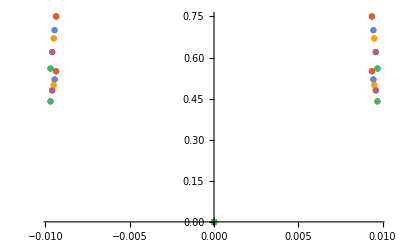

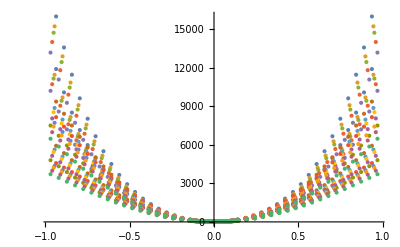

```mathematica
m={12.0107,91.224,1};kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;
(*Data in*)
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
filesC={"C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805","C_4685_760_110","C_4730_1900_110","C_4759_2500_110","C_4801_3200_110","C_4850_3805_110","C_4685_760_111","C_4730_1900_111","C_4759_2500_111","C_4801_3200_111","C_4850_3805_111"};
filesZr={"Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805","Zr_4685_760_110","Zr_4730_1900_110","Zr_4759_2500_110","Zr_4801_3200_110","Zr_4850_3805_110","Zr_4685_760_111","Zr_4730_1900_111","Zr_4759_2500_111","zr_4801_3200_111","Zr_4850_3805_111"};
filesCh={"1.harm.C_4685_760","1.harm.C_4730_1900","1.harm.C_4759_2500","1.harm.C_4801_3200","1.harm.C_4850_3805","1.harm.C_4685_760_110","1.harm.C_4730_1900_110","1.harm.C_4759_2500_110","1.harm.C_4801_3200_110","1.harm.C_4850_3805_110","1.harm.C_4685_760_111","1.harm.C_4730_1900_111","1.harm.C_4759_2500_111","1.harm.C_4801_3200_111","1.harm.C_4850_3805_111"};
filesZrh={"1.harm.Zr_4685_760","1.harm.Zr_4730_1900","1.harm.Zr_4759_2500","1.harm.Zr_4801_3200","1.harm.Zr_4850_3805","1.harm.Zr_4685_760_110","1.harm.Zr_4730_1900_110","1.harm.Zr_4759_2500_110","1.harm.Zr_4801_3200_110","1.harm.Zr_4850_3805_110","1.harm.Zr_4685_760_111","1.harm.Zr_4730_1900_111","1.harm.Zr_4759_2500_111","1.harm.Zr_4801_3200_111","1.harm.Zr_4850_3805_111"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,15}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,15}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,15}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,15}];
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,15}]
V[1,4,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4},x],{i,1,15}]
V[1,6,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6},x],{i,1,15}]
V[1,8,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15}]
V[1,10,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15}]
V[1,12,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]

V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,15}]
V[2,4,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4},x],{i,1,15}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]
```

```mathematica
V[1,2,x][[1]]
V[1,6,x][[1]]
V[2,2,x][[1]]
V[2,6,x][[1]]
```

6264.46 x^2

6256.47 x^2+6879.88 x^4+1626.02 x^6

8542.44 x^2

8508.33 x^2+8953.3 x^4+2418.13 x^6

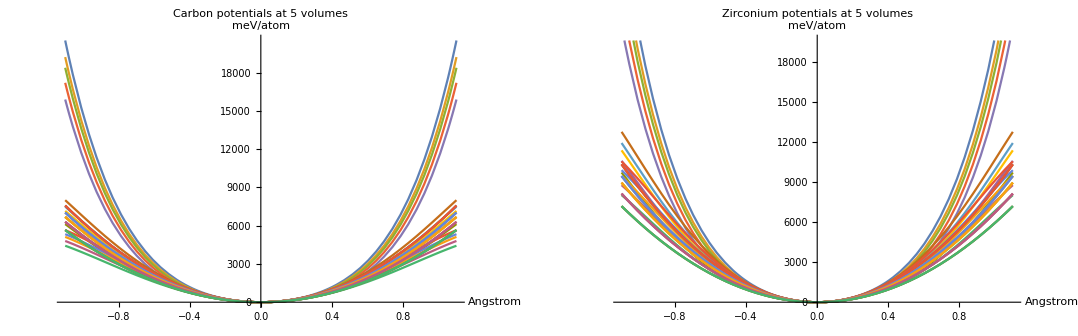

```mathematica
GraphicsGrid[{{Show[Plot[Evaluate@V[1,6,x],{x,-1.1,1.1},PlotRange->All,PlotLabel->"Carbon potentials at 5 volumes",AxesLabel->{"Angstrom","meV/atom"},ImageSize->500],Plot[Evaluate@V[1,2,x],{x,-1.1,1.1}]],Show[Plot[Evaluate@V[2,6,x],{x,-1.1,1.1},PlotLabel->"Zirconium potentials at 5 volumes",AxesLabel->{"Angstrom","meV/atom"},ImageSize->500],Plot[Evaluate@V[2,2,x],{x,-1.1,1.1}]]}}]
```

```mathematica
GraphicsGrid[{{Show[Plot[Evaluate@{V[2,2,x][[1]],V[2,12,x][[1]],V[2,12,x][[6]],V[2,12,x][[11]]},{x,-1,1},PlotLegends->SwatchLegend[{"harmonic","100 anharmonic","110 anharmonic","111 anharmonic"}],PlotLabel->"Carbon potentials at 4.685Angstrom",AxesLabel->{"Angstrom","meV/atom"}],ImageSize->500],Show[Plot[Evaluate@{V[1,2,x][[1]],V[1,12,x][[1]],V[1,12,x][[6]],V[1,12,x][[11]]},{x,-1,1},PlotLegends->SwatchLegend[{"harmonic","100 anharmonic","110 anharmonic","111 anharmonic"}],PlotLabel->"Zirconium potentials at 4.685Angstrom",AxesLabel->{"Angstrom","meV/atom"}],ImageSize->500]}},ImageSize->1300]
```

-Graphics-

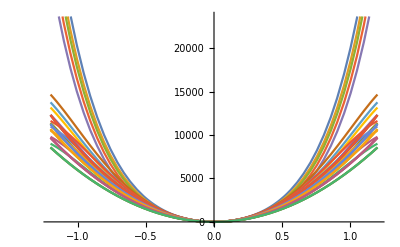

```mathematica
Show[Plot[Evaluate@V[2,6,x],{x,-1.2,1.2}],Plot[Evaluate@V[2,2,x],{x,-1.2,1.2}]]
```

```mathematica
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=Table[V[1,2,x][[i]][[1]],{i,1,5}]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=Table[V[2,2,x][[i]][[1]],{i,1,5}]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{6264.46,5810.6,5528.52,5208.33,4676.37}

cOmega0 in meV/Ang**2/AMU is approximately

{32.2978,31.1058,30.3414,29.4497,27.9052}

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{8542.44,7821.96,7408.22,6727.43,5951.75}

Z_Omega_0 in meV/Ang**2/AMU is approximately

{13.6852,13.0954,12.7443,12.1447,11.4231}

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first x eigenvalues and eigenvectors*)
Neigenvalues=200;
(*Define bounds for plotting and solving eigenproblem*)
B=1;H=2000;
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒallc=Table[-(1/(2m[[1]]))*u''[x]+V[1,2i,x]*u[x],{i,1,6,1}];
(*Zirconium Hamiltonians - harmonic, even symmetry to 12th order*)
ℒallz=Table[-(1/(2m[[2]]))*u''[x]+V[2,2i,x]*u[x],{i,1,6,1}];
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}};
```

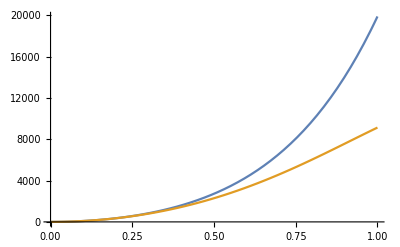

```mathematica
Plot[{Evaluate@V[2,6,x][[1]],Evaluate@V[2,6,x][[11]]},{x,0,1}]
```

```mathematica
V[2,2,x][[1]]
V[2,2,x][[6]]
```

8542.44 x^2

8542.44 x^2

```mathematica
α
```

√(x^2)

```mathematica
\[Alpha
```

```mathematica
Clear[alpha,beta,gamma]
V[2,4,α][[1]]
V[2,4,β][[6]]
V[2,4,γ][[11]]
```

Fit[{{-0.937,15994.9},{-0.89015,13579.2},{-0.8433,11460},{-0.79645,9619.58},{-0.7496,8032.41},{-0.70275,6669.55},{-0.6559,5502.69},{-0.60905,4506.13},{-0.5622,3657.23},{-0.51535,2936.34},{-0.4685,2326.47},{-0.42165,1812.97},{-0.3748,1383.3},{-0.32795,1026.73},{-0.2811,734.28},{-0.23425,498.43},{-0.1874,313.11},{-0.14055,173.62},{-0.13118,150.88},{-0.12181,129.81},{-0.11244,110.38},{-0.10307,92.58},{-0.0937,76.38},{-0.08433,61.77},{-0.07496,48.74},{-0.06559,37.27},{-0.05622,27.35},{-0.04685,18.98},{-0.03748,12.13},{-0.02811,6.82},{-0.01874,3.03},{-0.00937,0.75},{0,0},{0,0},{0.00937,0.75},{0.01874,3.03},{0.02811,6.82},{0.03748,12.13},{0.04685,18.98},{0.05622,27.35},{0.06559,37.27},{0.07496,48.74},{0.08433,61.77},{0.0937,76.38},{0.10307,92.58},{0.11244,110.38},{0.12181,129.81},{0.13118,150.88},{0.14055,173.62},{0.1874,313.11},{0.23425,498.43},{0.2811,734.28},{0.32795,1026.73},{0.3748,1383.3},{0.42165,1812.97},{0.4685,2326.47},{0.51535,2936.34},{0.5622,3657.23},{0.60905,4506.13},{0.6559,5502.69},{0.70275,6669.55},{0.7496,8032.41},{0.79645,9619.58},{0.8433,11460},{0.89015,13579.2},{0.937,15994.9}},{x^2,x^4},√(x^2)]

Fit[{{-0.937,9368.84},{-0.89015,8418.95},{-0.8433,7501.04},{-0.79645,6625.98},{-0.7496,5801.1},{-0.70275,5031.51},{-0.6559,4320.34},{-0.60905,3669.1},{-0.5622,3077.93},{-0.51535,2546.02},{-0.4685,2071.81},{-0.42165,1653.2},{-0.3748,1287.8},{-0.32795,973.06},{-0.2811,706.44},{-0.23425,485.49},{-0.1874,308},{-0.14055,172.04},{-0.13118,149.69},{-0.12181,128.93},{-0.11244,109.75},{-0.10307,92.13},{-0.0937,76.07},{-0.08433,61.57},{-0.07496,48.61},{-0.06559,37.2},{-0.05622,27.31},{-0.04685,18.96},{-0.03748,12.13},{-0.02811,6.82},{-0.01874,3.03},{-0.00937,0.75},{0,0},{0,0},{0.00937,0.75},{0.01874,3.03},{0.02811,6.82},{0.03748,12.13},{0.04685,18.96},{0.05622,27.31},{0.06559,37.2},{0.07496,48.61},{0.08433,61.57},{0.0937,76.07},{0.10307,92.13},{0.11244,109.75},{0.12181,128.93},{0.13118,149.69},{0.14055,172.04},{0.1874,308},{0.23425,485.49},{0.2811,706.44},{0.32795,973.06},{0.3748,1287.8},{0.42165,1653.2},{0.4685,2071.81},{0.51535,2546.02},{0.5622,3077.93},{0.60905,3669.1},{0.6559,4320.34},{0.70275,5031.51},{0.7496,5801.1},{0.79645,6625.98},{0.8433,7501.04},{0.89015,8418.95},{0.937,9368.84}},{1/2 (x^2+y^2),1/4 (x^2+y^2)^2},(√(x^2+y^2))/(√2)]

Fit[{{-0.937,8154.22},{-0.89015,7414.74},{-0.8433,6685.5},{-0.79645,5975.38},{-0.7496,5291.76},{-0.70275,4640.68},{-0.6559,4026.83},{-0.60905,3453.8},{-0.5622,2924.1},{-0.51535,2439.33},{-0.4685,2000.34},{-0.42165,1607.25},{-0.3748,1259.71},{-0.32795,956.92},{-0.2811,697.9},{-0.23425,481.45},{-0.1874,306.37},{-0.14055,171.54},{-0.13118,149.32},{-0.12181,128.64},{-0.11244,109.54},{-0.10307,91.98},{-0.0937,75.97},{-0.08433,61.5},{-0.07496,48.57},{-0.06559,37.17},{-0.05622,27.3},{-0.04685,18.95},{-0.03748,12.12},{-0.02811,6.82},{-0.01874,3.03},{-0.00937,0.75},{0,0},{0,0},{0.00937,0.75},{0.01874,3.03},{0.02811,6.82},{0.03748,12.12},{0.04685,18.95},{0.05622,27.3},{0.06559,37.17},{0.07496,48.57},{0.08433,61.5},{0.0937,75.97},{0.10307,91.98},{0.11244,109.54},{0.12181,128.64},{0.13118,149.32},{0.14055,171.54},{0.1874,306.37},{0.23425,481.45},{0.2811,697.9},{0.32795,956.92},{0.3748,1259.71},{0.42165,1607.25},{0.4685,2000.34},{0.51535,2439.33},{0.5622,2924.1},{0.60905,3453.8},{0.6559,4026.83},{0.70275,4640.68},{0.7496,5291.76},{0.79645,5975.38},{0.8433,6685.5},{0.89015,7414.74},{0.937,8154.22}},{1/3 (x^2+y^2+z^2),1/9 (x^2+y^2+z^2)^2},(√(x^2+y^2+z^2))/(√3)]

```mathematica
VC[2,4,x,y,z,1]=V[2,4,α][[1]]/.α->{x,y,z};
VC[2,4,x,y,z,1]
Total@VC[2,4,x,y,z,1]
```

Fit[{{-0.937,15994.9},{-0.89015,13579.2},{-0.8433,11460},{-0.79645,9619.58},{-0.7496,8032.41},{-0.70275,6669.55},{-0.6559,5502.69},{-0.60905,4506.13},{-0.5622,3657.23},{-0.51535,2936.34},{-0.4685,2326.47},{-0.42165,1812.97},{-0.3748,1383.3},{-0.32795,1026.73},{-0.2811,734.28},{-0.23425,498.43},{-0.1874,313.11},{-0.14055,173.62},{-0.13118,150.88},{-0.12181,129.81},{-0.11244,110.38},{-0.10307,92.58},{-0.0937,76.38},{-0.08433,61.77},{-0.07496,48.74},{-0.06559,37.27},{-0.05622,27.35},{-0.04685,18.98},{-0.03748,12.13},{-0.02811,6.82},{-0.01874,3.03},{-0.00937,0.75},{0,0},{0,0},{0.00937,0.75},{0.01874,3.03},{0.02811,6.82},{0.03748,12.13},{0.04685,18.98},{0.05622,27.35},{0.06559,37.27},{0.07496,48.74},{0.08433,61.77},{0.0937,76.38},{0.10307,92.58},{0.11244,110.38},{0.12181,129.81},{0.13118,150.88},{0.14055,173.62},{0.1874,313.11},{0.23425,498.43},{0.2811,734.28},{0.32795,1026.73},{0.3748,1383.3},{0.42165,1812.97},{0.4685,2326.47},{0.51535,2936.34},{0.5622,3657.23},{0.60905,4506.13},{0.6559,5502.69},{0.70275,6669.55},{0.7496,8032.41},{0.79645,9619.58},{0.8433,11460},{0.89015,13579.2},{0.937,15994.9}},{x^2,x^4},{x,y,z}]

Total[Fit[{{-0.937,15994.9},{-0.89015,13579.2},{-0.8433,11460},{-0.79645,9619.58},{-0.7496,8032.41},{-0.70275,6669.55},{-0.6559,5502.69},{-0.60905,4506.13},{-0.5622,3657.23},{-0.51535,2936.34},{-0.4685,2326.47},{-0.42165,1812.97},{-0.3748,1383.3},{-0.32795,1026.73},{-0.2811,734.28},{-0.23425,498.43},{-0.1874,313.11},{-0.14055,173.62},{-0.13118,150.88},{-0.12181,129.81},{-0.11244,110.38},{-0.10307,92.58},{-0.0937,76.38},{-0.08433,61.77},{-0.07496,48.74},{-0.06559,37.27},{-0.05622,27.35},{-0.04685,18.98},{-0.03748,12.13},{-0.02811,6.82},{-0.01874,3.03},{-0.00937,0.75},{0,0},{0,0},{0.00937,0.75},{0.01874,3.03},{0.02811,6.82},{0.03748,12.13},{0.04685,18.98},{0.05622,27.35},{0.06559,37.27},{0.07496,48.74},{0.08433,61.77},{0.0937,76.38},{0.10307,92.58},{0.11244,110.38},{0.12181,129.81},{0.13118,150.88},{0.14055,173.62},{0.1874,313.11},{0.23425,498.43},{0.2811,734.28},{0.32795,1026.73},{0.3748,1383.3},{0.42165,1812.97},{0.4685,2326.47},{0.51535,2936.34},{0.5622,3657.23},{0.60905,4506.13},{0.6559,5502.69},{0.70275,6669.55},{0.7496,8032.41},{0.79645,9619.58},{0.8433,11460},{0.89015,13579.2},{0.937,15994.9}},{x^2,x^4},{x,y,z}]]

```mathematica
VC[2,4,x,y,z,6]=V[2,4,β][[6]]/.β->{(1/Sqrt[2])*Sqrt[(x^2+y^2)],(1/Sqrt[2])*Sqrt[(y^2+z^2)],(1/Sqrt[2])*Sqrt[(z^2+x^2)]}//Expand;
VC[2,4,x,y,z,6]
Total@VC[2,4,x,y,z,6]
```

Fit[{{-0.937,9368.84},{-0.89015,8418.95},{-0.8433,7501.04},{-0.79645,6625.98},{-0.7496,5801.1},{-0.70275,5031.51},{-0.6559,4320.34},{-0.60905,3669.1},{-0.5622,3077.93},{-0.51535,2546.02},{-0.4685,2071.81},{-0.42165,1653.2},{-0.3748,1287.8},{-0.32795,973.06},{-0.2811,706.44},{-0.23425,485.49},{-0.1874,308},{-0.14055,172.04},{-0.13118,149.69},{-0.12181,128.93},{-0.11244,109.75},{-0.10307,92.13},{-0.0937,76.07},{-0.08433,61.57},{-0.07496,48.61},{-0.06559,37.2},{-0.05622,27.31},{-0.04685,18.96},{-0.03748,12.13},{-0.02811,6.82},{-0.01874,3.03},{-0.00937,0.75},{0,0},{0,0},{0.00937,0.75},{0.01874,3.03},{0.02811,6.82},{0.03748,12.13},{0.04685,18.96},{0.05622,27.31},{0.06559,37.2},{0.07496,48.61},{0.08433,61.57},{0.0937,76.07},{0.10307,92.13},{0.11244,109.75},{0.12181,128.93},{0.13118,149.69},{0.14055,172.04},{0.1874,308},{0.23425,485.49},{0.2811,706.44},{0.32795,973.06},{0.3748,1287.8},{0.42165,1653.2},{0.4685,2071.81},{0.51535,2546.02},{0.5622,3077.93},{0.60905,3669.1},{0.6559,4320.34},{0.70275,5031.51},{0.7496,5801.1},{0.79645,6625.98},{0.8433,7501.04},{0.89015,8418.95},{0.937,9368.84}},{1/2 (x^2+y^2),1/4 (x^2+y^2)^2},{(√(x^2+y^2))/(√2),(√(y^2+z^2))/(√2),(√(x^2+z^2))/(√2)}]

Total[Fit[{{-0.937,9368.84},{-0.89015,8418.95},{-0.8433,7501.04},{-0.79645,6625.98},{-0.7496,5801.1},{-0.70275,5031.51},{-0.6559,4320.34},{-0.60905,3669.1},{-0.5622,3077.93},{-0.51535,2546.02},{-0.4685,2071.81},{-0.42165,1653.2},{-0.3748,1287.8},{-0.32795,973.06},{-0.2811,706.44},{-0.23425,485.49},{-0.1874,308},{-0.14055,172.04},{-0.13118,149.69},{-0.12181,128.93},{-0.11244,109.75},{-0.10307,92.13},{-0.0937,76.07},{-0.08433,61.57},{-0.07496,48.61},{-0.06559,37.2},{-0.05622,27.31},{-0.04685,18.96},{-0.03748,12.13},{-0.02811,6.82},{-0.01874,3.03},{-0.00937,0.75},{0,0},{0,0},{0.00937,0.75},{0.01874,3.03},{0.02811,6.82},{0.03748,12.13},{0.04685,18.96},{0.05622,27.31},{0.06559,37.2},{0.07496,48.61},{0.08433,61.57},{0.0937,76.07},{0.10307,92.13},{0.11244,109.75},{0.12181,128.93},{0.13118,149.69},{0.14055,172.04},{0.1874,308},{0.23425,485.49},{0.2811,706.44},{0.32795,973.06},{0.3748,1287.8},{0.42165,1653.2},{0.4685,2071.81},{0.51535,2546.02},{0.5622,3077.93},{0.60905,3669.1},{0.6559,4320.34},{0.70275,5031.51},{0.7496,5801.1},{0.79645,6625.98},{0.8433,7501.04},{0.89015,8418.95},{0.937,9368.84}},{1/2 (x^2+y^2),1/4 (x^2+y^2)^2},{(√(x^2+y^2))/(√2),(√(y^2+z^2))/(√2),(√(x^2+z^2))/(√2)}]]

```mathematica
VC[2,4,X,Y,Z,11]=V[2,4,γ][[11]]/.γ->{(1/Sqrt[3])*Sqrt[(x^2+y^2+z^3)],(1/Sqrt[3])*Sqrt[(x^2+y^2+z^3)],(1/Sqrt[3])*Sqrt[(x^2+y^2+z^3)]}//Expand;
VC[2,4,X,Y,Z,11]
Even[Total[VC[2,4,X,Y,Z,11]]]
```

Fit[{{-0.937,8154.22},{-0.89015,7414.74},{-0.8433,6685.5},{-0.79645,5975.38},{-0.7496,5291.76},{-0.70275,4640.68},{-0.6559,4026.83},{-0.60905,3453.8},{-0.5622,2924.1},{-0.51535,2439.33},{-0.4685,2000.34},{-0.42165,1607.25},{-0.3748,1259.71},{-0.32795,956.92},{-0.2811,697.9},{-0.23425,481.45},{-0.1874,306.37},{-0.14055,171.54},{-0.13118,149.32},{-0.12181,128.64},{-0.11244,109.54},{-0.10307,91.98},{-0.0937,75.97},{-0.08433,61.5},{-0.07496,48.57},{-0.06559,37.17},{-0.05622,27.3},{-0.04685,18.95},{-0.03748,12.12},{-0.02811,6.82},{-0.01874,3.03},{-0.00937,0.75},{0,0},{0,0},{0.00937,0.75},{0.01874,3.03},{0.02811,6.82},{0.03748,12.12},{0.04685,18.95},{0.05622,27.3},{0.06559,37.17},{0.07496,48.57},{0.08433,61.5},{0.0937,75.97},{0.10307,91.98},{0.11244,109.54},{0.12181,128.64},{0.13118,149.32},{0.14055,171.54},{0.1874,306.37},{0.23425,481.45},{0.2811,697.9},{0.32795,956.92},{0.3748,1259.71},{0.42165,1607.25},{0.4685,2000.34},{0.51535,2439.33},{0.5622,2924.1},{0.60905,3453.8},{0.6559,4026.83},{0.70275,4640.68},{0.7496,5291.76},{0.79645,5975.38},{0.8433,6685.5},{0.89015,7414.74},{0.937,8154.22}},{1/3 (x^2+y^2+z^2),1/9 (x^2+y^2+z^2)^2},{(√(x^2+y^2+z^3))/(√3),(√(x^2+y^2+z^3))/(√3),(√(x^2+y^2+z^3))/(√3)}]

Even[Total[Fit[{{-0.937,8154.22},{-0.89015,7414.74},{-0.8433,6685.5},{-0.79645,5975.38},{-0.7496,5291.76},{-0.70275,4640.68},{-0.6559,4026.83},{-0.60905,3453.8},{-0.5622,2924.1},{-0.51535,2439.33},{-0.4685,2000.34},{-0.42165,1607.25},{-0.3748,1259.71},{-0.32795,956.92},{-0.2811,697.9},{-0.23425,481.45},{-0.1874,306.37},{-0.14055,171.54},{-0.13118,149.32},{-0.12181,128.64},{-0.11244,109.54},{-0.10307,91.98},{-0.0937,75.97},{-0.08433,61.5},{-0.07496,48.57},{-0.06559,37.17},{-0.05622,27.3},{-0.04685,18.95},{-0.03748,12.12},{-0.02811,6.82},{-0.01874,3.03},{-0.00937,0.75},{0,0},{0,0},{0.00937,0.75},{0.01874,3.03},{0.02811,6.82},{0.03748,12.12},{0.04685,18.95},{0.05622,27.3},{0.06559,37.17},{0.07496,48.57},{0.08433,61.5},{0.0937,75.97},{0.10307,91.98},{0.11244,109.54},{0.12181,128.64},{0.13118,149.32},{0.14055,171.54},{0.1874,306.37},{0.23425,481.45},{0.2811,697.9},{0.32795,956.92},{0.3748,1259.71},{0.42165,1607.25},{0.4685,2000.34},{0.51535,2439.33},{0.5622,2924.1},{0.60905,3453.8},{0.6559,4026.83},{0.70275,4640.68},{0.7496,5291.76},{0.79645,5975.38},{0.8433,6685.5},{0.89015,7414.74},{0.937,8154.22}},{1/3 (x^2+y^2+z^2),1/9 (x^2+y^2+z^2)^2},{(√(x^2+y^2+z^3))/(√3),(√(x^2+y^2+z^3))/(√3),(√(x^2+y^2+z^3))/(√3)}]]]

```mathematica
2
```

2

```mathematica
Total[VC[2,4,X,Y,Z,11]]/.x->1
```

Total[Fit[{{-0.937,8154.22},{-0.89015,7414.74},{-0.8433,6685.5},{-0.79645,5975.38},{-0.7496,5291.76},{-0.70275,4640.68},{-0.6559,4026.83},{-0.60905,3453.8},{-0.5622,2924.1},{-0.51535,2439.33},{-0.4685,2000.34},{-0.42165,1607.25},{-0.3748,1259.71},{-0.32795,956.92},{-0.2811,697.9},{-0.23425,481.45},{-0.1874,306.37},{-0.14055,171.54},{-0.13118,149.32},{-0.12181,128.64},{-0.11244,109.54},{-0.10307,91.98},{-0.0937,75.97},{-0.08433,61.5},{-0.07496,48.57},{-0.06559,37.17},{-0.05622,27.3},{-0.04685,18.95},{-0.03748,12.12},{-0.02811,6.82},{-0.01874,3.03},{-0.00937,0.75},{0,0},{0,0},{0.00937,0.75},{0.01874,3.03},{0.02811,6.82},{0.03748,12.12},{0.04685,18.95},{0.05622,27.3},{0.06559,37.17},{0.07496,48.57},{0.08433,61.5},{0.0937,75.97},{0.10307,91.98},{0.11244,109.54},{0.12181,128.64},{0.13118,149.32},{0.14055,171.54},{0.1874,306.37},{0.23425,481.45},{0.2811,697.9},{0.32795,956.92},{0.3748,1259.71},{0.42165,1607.25},{0.4685,2000.34},{0.51535,2439.33},{0.5622,2924.1},{0.60905,3453.8},{0.6559,4026.83},{0.70275,4640.68},{0.7496,5291.76},{0.79645,5975.38},{0.8433,6685.5},{0.89015,7414.74},{0.937,8154.22}},{1/3 (1+y^2+z^2),1/9 (1+y^2+z^2)^2},{(√(1+y^2+z^3))/(√3),(√(1+y^2+z^3))/(√3),(√(1+y^2+z^3))/(√3)}]]

```mathematica
alpha=(1/Sqrt[2])*Sqrt[(x^2+y^2)]
alpha^4//Expand
```

(√(x^2+y^2))/(√2)

x^4/4+(x^2 y^2)/2+y^4/4

```mathematica
beta=(1/Sqrt[3])*Sqrt[(x^2+y^2+z^2)]
beta^2//Expand
beta^4//Expand
```

(√(x^2+y^2+z^2))/(√3)

x^2/3+y^2/3+z^2/3

x^4/9+(2 x^2 y^2)/9+y^4/9+(2 x^2 z^2)/9+(2 y^2 z^2)/9+z^4/9

```mathematica
(x+y)^4//Expand
```

x^4+4 x^3 y+6 x^2 y^2+4 x y^3+y^4

```mathematica
(x+y+z)^4//Expand
```

x^4+4 x^3 y+6 x^2 y^2+4 x y^3+y^4+4 x^3 z+12 x^2 y z+12 x y^2 z+4 y^3 z+6 x^2 z^2+12 x y z^2+6 y^2 z^2+4 x z^3+4 y z^3+z^4

```mathematica
a=V[2,6,x][[1]]/.x->x
b=V[2,6,x][[1]]/.x->y
c=V[2,6,x][[11]]/.x->x+y
d=V[2,6,x][[11]]/.x->x-y
```

8508.33 x^2+8953.3 x^4+2418.13 x^6

8508.33 y^2+8953.3 y^4+2418.13 y^6

8674.74 (x+y)^2+2437.17 (x+y)^4-1984.51 (x+y)^6

8674.74 (x-y)^2+2437.17 (x-y)^4-1984.51 (x-y)^6

```mathematica
Plot3D[{a,b,c,d},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Clear[a,b]
r=1/Sqrt[2];
Manipulate[ContourPlot3D[{0.1(x*x+y*y+z*z)+aa*(x*x+y*y+z*z)^2+bb*(x^2y^2+y^2 z^2 +z^2 x^2)},{x,-r,r},{y,-r,r},{z,-r,r},Contours->1],{aa,-0.5,0.5},{bb,-0.5,0.5}]
aa//N
```

aa

ContourPlot3D::plln: Limiting value -r in {x,-r,r} is not a machine-sized real number.

```mathematica
ContourPlot3D[{0.1(x*x+y*y+z*z)+0.74(x*x+y*y+z*z)^2+-2.2*(x^2y^2+y^2 z^2 +z^2 x^2)},{x,-r,r},{y,-r,r},{z,-r,r},Contours->1]
```

-Graphics3D-

```mathematica
ContourPlot3D[{0.1(x*x+y*y+z*z)+0.74(x*x+y*y+z*z)^2-2.2*(x^2y^2+y^2 z^2 +z^2 x^2)},{x,-r,r},{y,-r,r},{z,-r,r},Contours->1]
```

-Graphics3D-

```mathematica
ContourPlot3D[{0.05(x*x+y*y+z*z)+0.2(x*x+y*y+z*z)^3+0(x^4*y^2+y^4*z^2+z^4*x^2)},{x,-r,r},{y,-r,r},{z,-r,r},Contours->1]/.r->2
```

-Graphics3D-

```mathematica
(a*x*x+b*y*y+c*z*z)^3
```

(a x^2+b y^2+(8674.74 (x+y)^2+2437.17 (x+y)^4-1984.51 (x+y)^6) z^2)^3

```mathematica
(*X[2,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[2,1,θ,ϕ]-SphericalHarmonicY[2,-1,θ,ϕ])
X[3,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[2,2,θ,ϕ]-SphericalHarmonicY[2,-2,θ,ϕ])
X[4,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[2,1,θ,ϕ]+SphericalHarmonicY[2,-1,θ,ϕ])
X[5,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ])

X[2,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[2,1,θ,ϕ]-SphericalHarmonicY[2,-1,θ,ϕ])
X[3,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[2,2,θ,ϕ]-SphericalHarmonicY[2,-2,θ,ϕ])*)
```

```mathematica
(*Kubic harmonics can be expressed as a linear combination of spherical harmonics:
X=Y0
X'=1/sqrt[2] * (Ylm-Yl-m)
X''=1/sqrt[2] * (Ylm+Yl-m)*)
```

```mathematica
(*Real linear combinations of spherical harmonics invariant on cube*)
X[1,θ,ϕ]:=SphericalHarmonicY[2,0,θ,ϕ]
X[2,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ])

X[3,θ,ϕ]:=SphericalHarmonicY[4,0,θ,ϕ]
X[4,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[4,2,θ,ϕ]+SphericalHarmonicY[4,-2,θ,ϕ])
X[5,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[4,4,θ,ϕ]+SphericalHarmonicY[4,-4,θ,ϕ])

X[6,θ,ϕ]:=SphericalHarmonicY[6,0,θ,ϕ]
X[7,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[6,2,θ,ϕ]+SphericalHarmonicY[6,-2,θ,ϕ])
X[8,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[6,4,θ,ϕ]+SphericalHarmonicY[6,-4,θ,ϕ])
X[9,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[6,6,θ,ϕ]+SphericalHarmonicY[6,-6,θ,ϕ])

(*https://en.wikipedia.org/wiki/Table_of_spherical_harmonics*)
```

```mathematica
Table[Abs@X[i,θ,ϕ]//Simplify,{i,1,5}]//TableForm
```

1/4 √(5/π) Abs[1-3 Cos[θ]^2]
1/8 ⅇ^(2 Im[ϕ]) √(15/π) Abs[(1+ⅇ^(4 ⅈ ϕ)) Sin[θ]^2]
(3 Abs[3-30 Cos[θ]^2+35 Cos[θ]^4])/(16 √π)
3/32 ⅇ^(2 Im[ϕ]) √(5/π) Abs[(1+ⅇ^(4 ⅈ ϕ)) (5+7 Cos[2 θ]) Sin[θ]^2]
3/32 ⅇ^(4 Im[ϕ]) √(35/π) Abs[(1+ⅇ^(8 ⅈ ϕ)) Sin[θ]^4]

```mathematica
SphericalPlot3D[Evaluate[Total[Table[Abs@X[j,θ,ϕ],{j,1,9}]]],{θ,0,Pi},{ϕ,0,2 Pi},PlotRange->All]
```

-Graphics3D-

```mathematica
NX[1,θ,ϕ]:=SphericalHarmonicY[2,0,θ,ϕ]/Sqrt[SphericalHarmonicY[2,0,θ,ϕ]^2]
NX[2,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ])/Abs[Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ])]

NX[3,θ,ϕ]:=SphericalHarmonicY[4,0,θ,ϕ]/Abs[SphericalHarmonicY[4,0,θ,ϕ]]
NX[4,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[4,2,θ,ϕ]+SphericalHarmonicY[4,-2,θ,ϕ])/Abs[Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[4,2,θ,ϕ]+SphericalHarmonicY[4,-2,θ,ϕ])]
NX[5,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[4,4,θ,ϕ]+SphericalHarmonicY[4,-4,θ,ϕ])/Abs[Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[4,4,θ,ϕ]+SphericalHarmonicY[4,-4,θ,ϕ])
]

NX[6,θ,ϕ]:=SphericalHarmonicY[6,0,θ,ϕ]/Abs[SphericalHarmonicY[6,0,θ,ϕ]]
NX[7,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[6,2,θ,ϕ]+SphericalHarmonicY[6,-2,θ,ϕ])/Abs[Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[6,2,θ,ϕ]+SphericalHarmonicY[6,-2,θ,ϕ])]
NX[8,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[6,4,θ,ϕ]+SphericalHarmonicY[6,-4,θ,ϕ])/Abs[Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[6,4,θ,ϕ]+SphericalHarmonicY[6,-4,θ,ϕ])]
NX[9,θ,ϕ]:=Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[6,6,θ,ϕ]+SphericalHarmonicY[6,-6,θ,ϕ])/Abs[Sqrt[-1]/Sqrt[2]*(SphericalHarmonicY[6,6,θ,ϕ]+SphericalHarmonicY[6,-6,θ,ϕ])]
```

```mathematica
GraphicsGrid[{Table[SphericalPlot3D[Evaluate[Total[Abs@NX[j,θ,ϕ]]],{θ,0,Pi},{ϕ,0,2 Pi},PlotRange->All],{j,1,1}]},ImageSize->200]
```

-Graphics-

```mathematica
SphericalPlot3D[Evaluate[Total[Table[NX[j,θ,ϕ],{j,1,1}]]],{θ,0,Pi},{ϕ,0,2 Pi},PlotRange->All]
```

-Graphics3D-

```mathematica
Clear[All]
```

```mathematica
γ
```

(√(x^2+y^2+z^2))/(√3)

Fit[{{-0.937,11900.9},{-0.89015,10080.9},{-0.8433,8509.98},{-0.79645,7151.89},{-0.7496,5978.36},{-0.70275,4966.37},{-0.6559,4096.42},{-0.60905,3351.42},{-0.5622,2716.03},{-0.51535,2176.53},{-0.4685,1720.66},{-0.42165,1337.63},{-0.3748,1018.02},{-0.32795,753.67},{-0.2811,537.64},{-0.23425,364.08},{-0.1874,228.24},{-0.14055,126.33},{-0.13118,109.75},{-0.12181,94.39},{-0.11244,80.24},{-0.10307,67.28},{-0.0937,55.5},{-0.08433,44.87},{-0.07496,35.4},{-0.06559,27.07},{-0.05622,19.86},{-0.04685,13.78},{-0.03748,8.81},{-0.02811,4.95},{-0.01874,2.2},{-0.00937,0.55},{0,0},{0,0},{0.00937,0.55},{0.01874,2.2},{0.02811,4.95},{0.03748,8.81},{0.04685,13.78},{0.05622,19.86},{0.06559,27.07},{0.07496,35.4},{0.08433,44.87},{0.0937,55.5},{0.10307,67.28},{0.11244,80.24},{0.12181,94.39},{0.13118,109.75},{0.14055,126.33},{0.1874,228.24},{0.23425,364.08},{0.2811,537.64},{0.32795,753.67},{0.3748,1018.02},{0.42165,1337.63},{0.4685,1720.66},{0.51535,2176.53},{0.5622,2716.03},{0.60905,3351.42},{0.6559,4096.42},{0.70275,4966.37},{0.7496,5978.36},{0.79645,7151.89},{0.8433,8509.98},{0.89015,10080.9},{0.937,11900.9}},{x^2,x^4},√(x^2)]

```mathematica
Clear[α,β,γ]
(*define 4th order potentials along 001 (alpha) 011 (beta) and 111 (gamma)*)
V[α_]:=V[1,6,α][[1]]
V[β_]:=V[1,6,β][[6]]
V[γ_]:=V[1,6,γ][[11]]
V[α]
V[β]
V[γ]
```

6282.42 α^2-921.722 α^4-341.247 α^6

6282.42 β^2-921.722 β^4-341.247 β^6

6282.42 γ^2-921.722 γ^4-341.247 γ^6

```mathematica
Clear[α,β,γ]
```

```mathematica
(*Express crystallographic directions in Cartesian coordinates*)
rule3={γ->(1/Sqrt[3])*Sqrt[(x^2+y^2+z^2)]}
```

{β→(√(x^2+y^2))/(√2),β→(√(x^2+y^2))/(√2)}

{γ→(√(x^2+y^2+z^2))/(√3)}

```mathematica
(*rule1={α->(1/Sqrt[1])*Sqrt[(x^2)],α->(1/Sqrt[1])*Sqrt[(y^2)]}
rule2={β->(1/Sqrt[2])*Sqrt[(x^2+y^2)],β->(1/Sqrt[2])*Sqrt[(x^2+y^2)]}*)
rule1={α->(x/Sqrt[1]),α->(y/Sqrt[1])}
rule2={β->((x+y)/Sqrt[2]),β->((+y-x)/Sqrt[2])}
```

{α→x,α→y}

{β→(x+y)/(√2),β→(-x+y)/(√2)}

```mathematica
U1[x_,y_]:=Sum[V[α]/.rule1[[i]],{i,1,2}]//Simplify
U2[x_,y_]:=Sum[V[β]/.rule2[[i]],{i,1,2}]//Simplify
UU[x,y]:=U1[x,y]+U2[x,y]
```

```mathematica
UU[x,y]
```

6282.42 x^2-921.722 x^4-341.247 x^6+3141.21 (x-1. y)^2-230.43 (x-1. y)^4-42.6559 (x-1. y)^6+6282.42 y^2-921.722 y^4-341.247 y^6+3141.21 (x+y)^2-230.43 (x+y)^4-42.6559 (x+y)^6

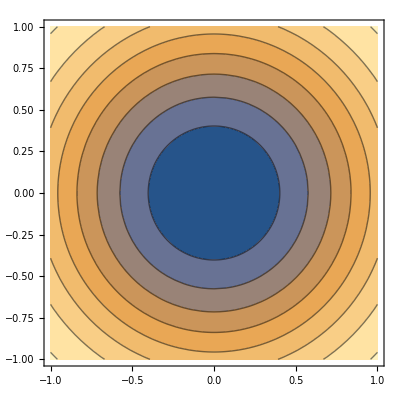

```mathematica
ContourPlot[U1[x,y]+U2[x,y],{x,-1,1},{y,-1,1}]
```

```mathematica
U1[x,y]//Expand
U2[x,y]//Expand
```

5774.79 x^2+8775.82 x^4+5774.79 y^2+8775.82 y^4

6483.37 x^2+172.751 x^4+6483.37 y^2+345.503 x^2 y^2+172.751 y^4

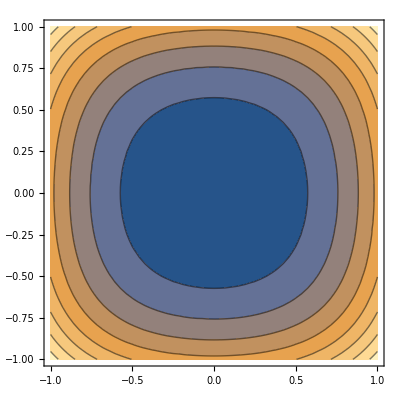

```mathematica
ContourPlot[U1[x,y]+U2[x,y],{x,-1,1},{y,-1,1}]
```

```mathematica
8775.819011023927 (x^4+y^4)-6483.365264460995 (x^2+y^2)-172.75127179438508 (x^2+y^2)^2
```

-6483.37 (x^2+y^2)-172.751 (x^2+y^2)^2+8775.82 (x^4+y^4)

```mathematica
U1[1,0]
U2[1,1]
```

14550.6

13657.7

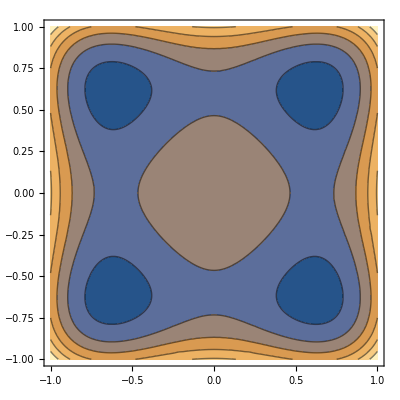

```mathematica
ContourPlot[-6483.365264460995 (x^2+y^2)-172.75127179438508 (x^2+y^2)^2+8775.819011023927 (x^4+y^4),{x,-1,1},{y,-1,1}]
```

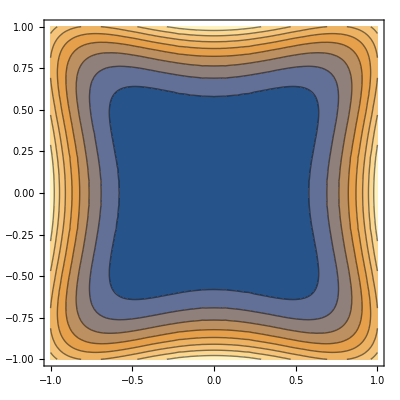

```mathematica
ContourPlot[8775.819011023927 (x^4+y^4)-10000x^2y^2,{x,-1,1},{y,-1,1}]
```

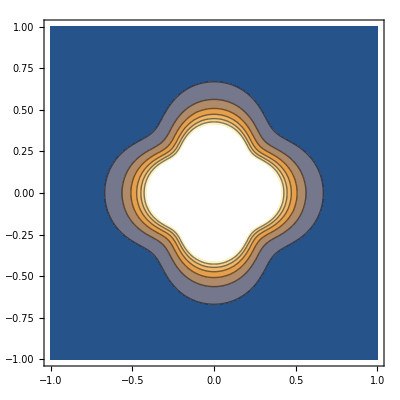

```mathematica
ContourPlot[(x^4(1-y^4/(Sqrt[x^2+y^2])^4)+y^4(1-x^4/(Sqrt[x^2+y^2])^4))/Sqrt[x^2+y^2]^8,{x,-1,1},{y,-1,1}]
```

```mathematica
ContourPlot3D[(x^4z^4(1-y^4/(Sqrt[x^2+y^2+z^2])^4)+y^4 z^4(1-x^4/(Sqrt[x^2+y^2+z^2])^4)+y^4 x^4(1-z^4/(Sqrt[x^2+y^2+z^2])^4))/Sqrt[x^2+y^2+z^2]^8,{x,-2,2},{y,-2,2},{z,-2,2}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics3D-

```mathematica
ContourPlot3D[(x^2z^2(1-y^2/(Sqrt[x^2+y^2+z^2])^2)+y^2 z^2(1-x^2/(Sqrt[x^2+y^2+z^2])^2)+y^2 x^2(1-z^2/(Sqrt[x^2+y^2+z^2])^2))/Sqrt[x^2+y^2+z^2]^4,{x,-2,2},{y,-2,2},{z,-2,2}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics3D-

```mathematica
ContourPlot3D[(x^2+y^2+z^2)/(Sqrt[x^2+y^2+z^2]^2)+(x^2z^2(1-y^2/(Sqrt[x^2+y^2+z^2])^2)+y^2 z^2(1-x^2/(Sqrt[x^2+y^2+z^2])^2)+y^2 x^2(1-z^2/(Sqrt[x^2+y^2+z^2])^2))/Sqrt[x^2+y^2+z^2]^4,{x,-2,2},{y,-2,2},{z,-2,2}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[(x^4z^4(1-y^4/(Sqrt[x^2+y^2+z^2])^4)+y^4 z^4(1-x^4/(Sqrt[x^2+y^2+z^2])^4)+y^4 x^4(1-z^4/(Sqrt[x^2+y^2+z^2])^4))/Sqrt[x^2+y^2+z^2]^8,{x,-1,1},{y,-1,1},{z,-1,1}]
```

Plot3D::nonopt: Options expected (instead of {z,-1,1}) beyond position 3 in Plot3D[(x^4 z^4 (1-Power[«2»] Power[«2»])+y^4 z^4 (1-Power[«2»] Power[«2»])+y^4 x^4 (1-Power[«2»] Power[«2»]))/((√(x^2+y^2+z^2))^8),{x,-1,1},{y,-1,1},{z,-1,1}]. An option must be a rule or a list of rules.

Plot3D[(x^4 z^4 (1-y^4/((√(x^2+y^2+z^2))^4))+y^4 z^4 (1-x^4/((√(x^2+y^2+z^2))^4))+y^4 x^4 (1-z^4/((√(x^2+y^2+z^2))^4)))/((√(x^2+y^2+z^2))^8),{x,-1,1},{y,-1,1},{z,-1,1}]